# Large-Amplitude Elongated-Body Theory of Fish Locomotion

## Lighthill’s Elongated-Body Theory (EBT)

Lighthill’s elongated-body theory makes use of three principles:
	(i) Water momentum near a section of fish is in a direction perpendicular to the backbone and has magnitude equal to the virtual mass, m per unit length, times the component w of fish velocity in that direction.
	(ii) Thrust can be obtained by considering rate of change of momentum within a volume enclosing the fish whose boundary at each instant includes a flat surface Π perpendicular to the caudal fin through its posterior end.
	(iii) In the momentum balance it is necessary to take into account transfer of momentum across Π not only by convection but also by the action of the resultant 1/2 mw^2of the pressures generated by the motions within the plane Π.

The coordinates used by Lighthill are:
•y-axis as the vertical
•x-axis and z-axis as the horizontal
•Lagrangian coordinate a along the fish body that takes values from 0 (tail) to l (head), the length of the fish
where a left-handed system of axes is used.	

In addition, we have several notation:
•(u,w) is the horizontal velocity vector (in the Lagrangian fish body frame), where u is the tangential component (forward direction) and w is the perpendicular component (lateral direction) of the fish body
•(P,Q) is the force vector where P is thrust and Q is sideforce; P is forward direction, Q is lateral direction
•V is the magnitude of the (u,w)
•W is the component perpendicular to the direction of mean motion
In an elongated body form, the virtual mass is large in respect of the w motions, while the u motions have negligible virtual mass.

The inextensibility of the fish’s spinal column requires ((∂x)/(∂a))^2+((∂z)/(∂a))^2=1. 
The horizontal velocity vector (in a left-handed x-z coordinate system) ((∂x)/(∂t),(∂z)/(∂t))has a tangential component (relative to the spinal column) u=(∂x)/(∂t)(∂x)/(∂a)+(∂z)/(∂t)(∂z)/(∂a)and a perpendicular component w=(∂z)/(∂t)(∂x)/(∂a)-(∂x)/(∂t)(∂z)/(∂a). 
The momentum per unit length of fish is represented by the vector mw(-(∂z)/(∂a),(∂x)/(∂a))where the factor in parentheses is a unit vector in the w-direction.
In general, 
(P,Q)=[mw((∂z)/(∂t),-(∂x)/(∂t))-1/2 mw^2((∂x)/(∂a),(∂z)/(∂a))]_(a=0)-d/dt∫_0^l mw(-(∂z)/(∂a),(∂x)/(∂a))ⅆa

### Analytical Computation

```mathematica
m=1/4 π*ρ*s^2;
```

```mathematica
{P1,Q1}=(m*w*{D[z,t],-D[x,t]}-1/2 m*w^2*{D[x,a],D[z,a]})
```

```mathematica
{P2, Q2}=D[Integrate[m*w*{-D[z,a],D[x,a]},{a,0,l}],t]
```

```mathematica
{P,Q}=({P1,Q1}/.a-> 0)-{P2, Q2}
```

## Borazjani and Sotiropoulos’ Carangiform Model

Two non-dimensional parameters that characterize the steady inline performance of a carangiform swimmer are the Reynolds number (Re) of the flow and the Strouhal number (St) of the undulatory body motion.
•L is the fish length
•U is the steady inline swimming speed
•v is the kinematic viscosity of the water
•A is the maximum lateral excursion of the tail over a cycle
•f is the tail beat frequency.
Most fishes have been shown swim near a ‘universal’ optimal value of 0.3.

### Fish body kinematics and non-dimensional parameters

The equation describing the lateral undulations of the fish body is given by

```mathematica
h[z_,t_]:=a[z]*Sin[k*z-ω*t]
```

where
•z is the axial (flow) direction measured along the fish axis from the tip of the fish head (essentially Lighthill’s x-coordinate)
•h(z,t) is the lateral (side-to-side) excursion at time t (essentially Lighthill’s z-coordinate)
•a(z) is the first Fourier coefficient defining the amplitude envelope of lateral motion as a function of z
•k is the wave number of the body undulations that corresponds to a wavelength λ
•ω is the angular frequency
The values given below were experimentally determined by Videler and Hess.

Table 1. Summaries of variables between Lighthill and Borazjani
Variable | Lighthill | Borazjani
a | Fish coordinate | First Fourier coefficient for amplitude envelope
h | □ | the lateral excursion
t | time | time
x | Horizontal coordinate along flow lines ( a,t) | □
y | Vertical coordinate | □
z | Horizontal Coord. perpendicular to flow (a,t) | Axial (flow) direction measured along the 
fish axis from the tip of the fish head;
u | Horizontal velocity vector (x dir in y=0 plane) | □
v | Vertical velocity vector in y=0 plane (z dir) | □
k | □ | WavenumberTable 2. Equivalent variables between the two papers
Lighhill | Borazjani
a | □
x | z
y | □
z | h
□ | □
□ | □
□ | □
□ | □
□ | □

```mathematica
Subscript[a, 0]=0.02;
Subscript[a, 1]=-0.08;
Subscript[a, 2]=0.16;
amax=0.1;
hmax=0.1 L;
λ/L=0.95;
```

Set::write: Tag Times in λ/L is Protected.

```mathematica
Reynolds=(L*U)/v;
Strouhals=2 f hmax;
a[z_]:=Subscript[a, 0]+Subscript[a, 1] z+Subscript[a, 2] z^2;
```

```mathematica
L=1;
k=(2*π)/(.95*L);
ω=(2*π*0.3)/(2*0.1);
```

```mathematica
Clear[z]
```

A plot of h[z,t] from z=0 to 1 for various values of t.

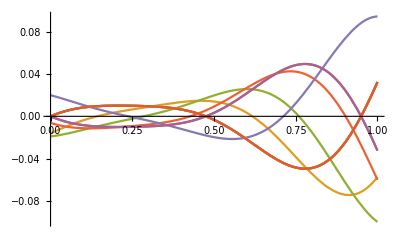

```mathematica
Plot[Evaluate[Table[h[z,t],{t,{0,0.1,0.2,0.3,0.5,1,2,4,9,10,20}}]],{z,0,1}]
```

### Attempting to relate coordinates

Trying to relate Borazjani’s h and z in terms of Lagrangian coordinate
Next time: plot s over t and see if it stays constant (preserves body length)

```mathematica
dHdZ[z_,t_]:=D[h[zz,t],zz] /.zz->z
```

A plot of dH/dZ at time 0:

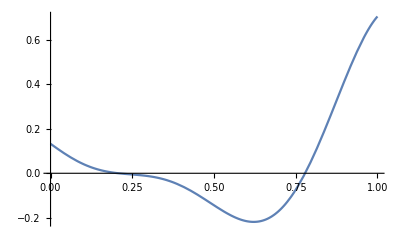

```mathematica
Plot[dHdZ[z,0],{z,0,1}]
```

```mathematica
dHdt[z_,t_]:=D[h[z,tt],tt] /. tt->t
```

A plot of dH/dt at time 0:

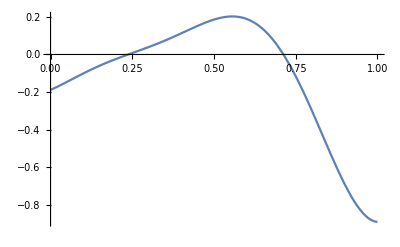

```mathematica
Plot[dHdt[z,0],{z,0,1}]
```

We want to confirm the inextensibility of the fish’s body length. In terms of Lighthill’s coordinates, we want to confirm that (dx/da)^2+(dz/da)^2=1. To find Lighthill’s dx/da (which in Borazjani’s coordinates, x is z), we will use 1/(√(1+(dH/dz)^2). Then, using the chain rule, we can find dz/da=dH/dz÷da/dz.

```mathematica
dxda[z_,t_]:=1/Sqrt[1+(dHdZ[z,t])^2]
```

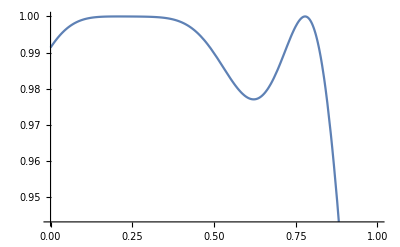

```mathematica
Plot[dxda[z,0],{z,0,1}]
```

```mathematica
dzda[z_,t_]:=dHdZ[z,t]*dxda[z,t]
```

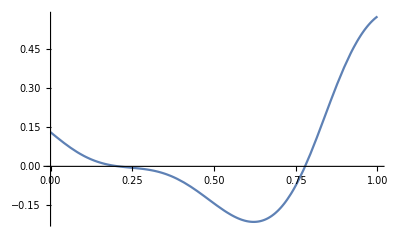

```mathematica
Plot[dzda[z,0],{z,0,1}]
```

Testing the inextensibility for various values of z and t, we see that it comes out to 1:

```mathematica
Table[(dxda[z,0])^2+(dzda[z,0])^2,{z,0,1,0.1}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Table[(dxda[z,2])^2+(dzda[z,2])^2,{z,0,1,0.1}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

From here, we can find the u and w vectors from Lighthill, which will let us find the momentum and force vectors.